# An Elementary Introduction to Wolfram Language

## Part 3

## 图形和网络

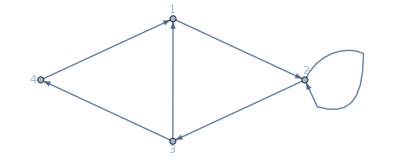

```mathematica
Graph[{1->2,2->3,3->4,4->1,3->1,2->2},VertexLabels->All,GraphLayout->"SpringElectricalEmbedding"]
```

找到从 4 到 2 的最短路径，始终遵循箭头

```mathematica
FindShortestPath[Graph[{1->2,2->3,3->4,4->1,3->1,2->2}],4,2]
```

{4,1,2}

全连接

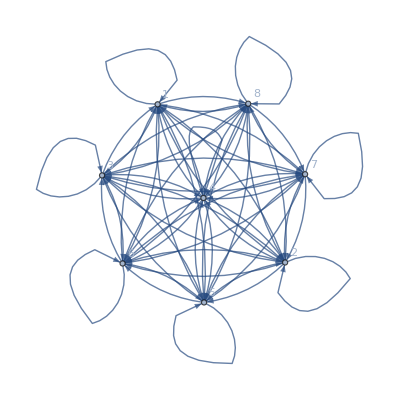

```mathematica
Graph[Flatten@Table[i->j,{i,8},{j,8}],VertexLabels->All]
```

随机连接

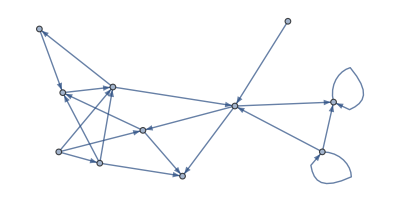
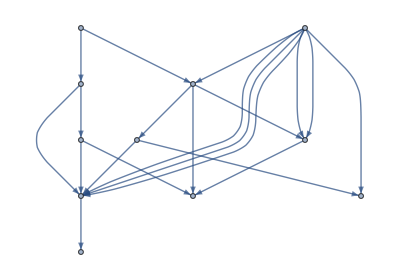
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Graph[Table[RandomInteger[10]->RandomInteger[10],20]],6]
```

分解“社区”

```mathematica
CommunityGraphPlot/@%
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

具有 100 个节点和 200 条边的随机图

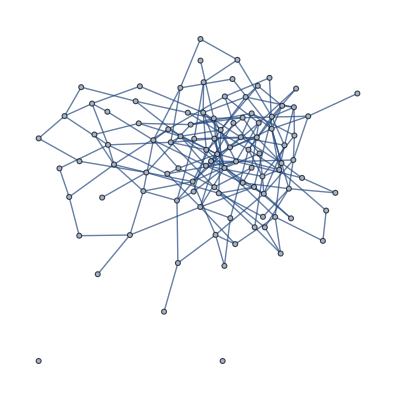

```mathematica
RandomGraph[{100,200}]
```

邻接矩阵

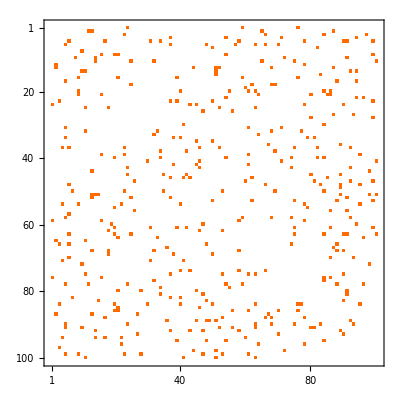

```mathematica
MatrixPlot@AdjacencyMatrix@%
```

## 机器学习

语言识别

```mathematica
LanguageIdentify[{"thank you","merci","dar las gracias","感謝","благодарить"}]
```

{English,French,Spanish,Chinese macrolanguage,Russian}

图像识别

```mathematica
ImageIdentify[-Graphics-]
```

rock dove

情感分类

```mathematica
Classify["Sentiment","I'm so happy to be programming"]
```

Positive

```mathematica
Classify["Sentiment","I'm so frustrated to be programming"]
```

Negative

训练一个分类器

```mathematica
Classify[{-Graphics- -> 0, -Graphics- -> 1, -Graphics- -> 0, -Graphics- -> 1, -Graphics- -> 1, -Graphics- -> 0, -Graphics- -> 0, -Graphics- -> 1, -Graphics- -> 1, -Graphics- -> 0, -Graphics- -> 0, -Graphics- -> 0, -Graphics- -> 1, -Graphics- -> 0, -Graphics- -> 1, -Graphics- -> 0, -Graphics- -> 1, -Graphics- -> 1, -Graphics- -> 1},
 -Graphics-]
```

0

最接近

```mathematica
Nearest[{10,20,30,40,50,60,70,80},22]
```

{20}

```mathematica
Nearest[{10,20,30,40,50,60,70,80},22,3]
```

{20,30,10}

```mathematica
Nearest[WordList[Language->"English"],"good",10]
```

{good,food,goad,god,gold,goo,goody,goof,goon,goop}

本质是“编辑距离”

```mathematica
EditDistance["AACCGGTT","AACCTTGG"]
```

4

识别文本

```mathematica
Table[Blur[Rasterize[Style["hello",15,FontFamily->"Algerian"]],r],{r,0,8}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
TextRecognize[#,Language->"English"]&/@%
```

{HELLO,HELLO,HELLO,HELLO,,,,,}

特征空间

```mathematica
FeatureSpacePlot[Rasterize/@Alphabet[]]
```

-Graphics-

```mathematica
FeatureSpacePlot[{-Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-}]
```

-Graphics-

## 关于数字

数值近似

```mathematica
N[2^1000]
```

1.07151×10^301

科学计数法

```mathematica
1.07*^301
```

1.07×10^301

Pi 的位数

```mathematica
N[Pi,250]
```

3.141592653589793238462643383279502884197169399375105820974944592307816406286208998628034825342117067982148086513282306647093844609550582231725359408128481117450284102701938521105559644622948954930381964428810975665933446128475648233786783165271201909

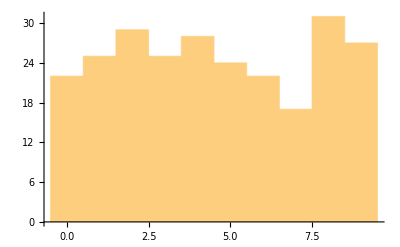

```mathematica
Histogram@First@RealDigits@%
```

前50个素数

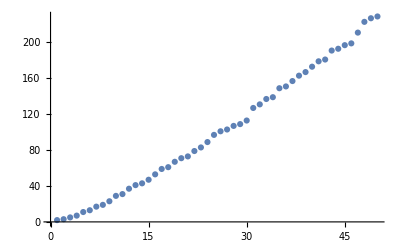

```mathematica
ListPlot[Prime/@Range[50]]
```

对数坐标轴展示相对大小

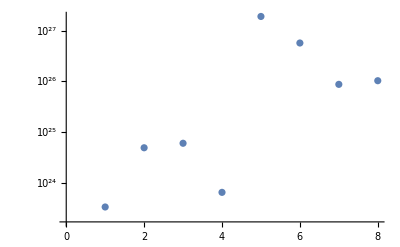

```mathematica
ListLogPlot[["Mass"]]
```

## 更多可视化格式

Mesh

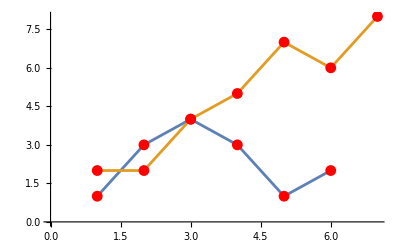

```mathematica
ListLinePlot[{{1,3,4,3,1,2},{2,2,4,5,7,6,8}},Mesh->All,MeshStyle->Red]
```

直方图用来可视化频次

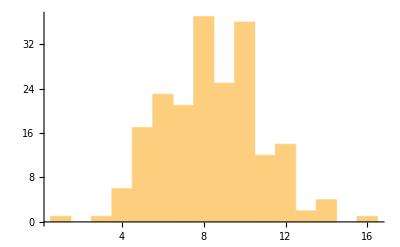

```mathematica
Histogram@StringLength@Take[WordList[Language->"English"],200]
```

所有单词的结果更为平滑

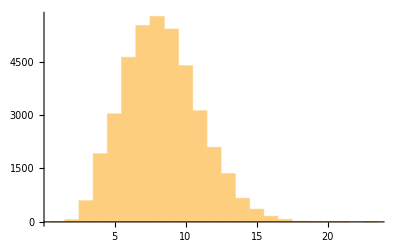

```mathematica
Histogram@StringLength@WordList[Language->"English"]
```

## 函数的应用方法

前缀式

```mathematica
ColorNegate@EdgeDetect@-Graphics-
```

-Graphics-

后缀式

```mathematica
-Graphics-//EdgeDetect//ColorNegate
```

-Graphics-

可列函数

```mathematica
Prime/@{10,100,1000,10000}
```

{29,541,7919,104729}

```mathematica
Prime[{10,100,1000,10000}]
```

{29,541,7919,104729}

不可列函数


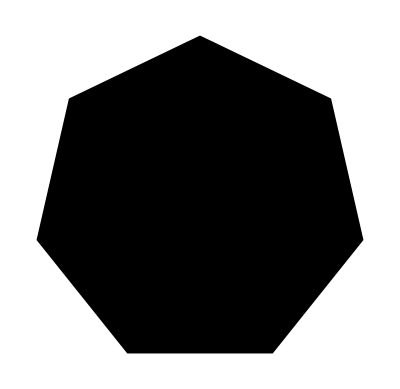
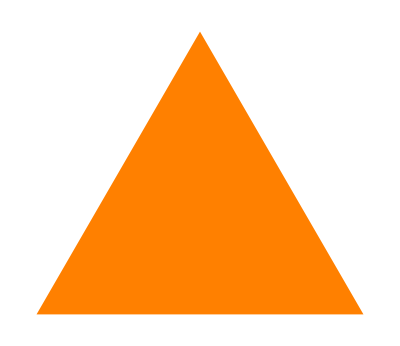

```mathematica
Graphics/@{Circle[],RegularPolygon[7],Style[RegularPolygon[3],Orange]}
```

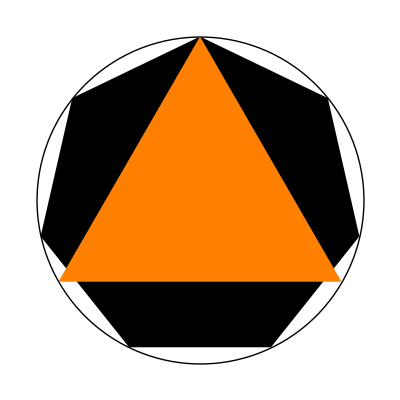

```mathematica
Graphics[{Circle[],RegularPolygon[7],Style[RegularPolygon[3],Orange]}]
```

## 纯函数

使用纯函数

```mathematica
Column[{#,ColorNegate[#],#}]&[Blend[{Red,Yellow}]]
```

RGBColor[1, Rational[1, 2], 0]
RGBColor[0., 0.5, 1.]
RGBColor[1, Rational[1, 2], 0]

不使用纯函数

```mathematica
Column[{Blend[{Red,Yellow}],ColorNegate[Blend[{Red,Yellow}]],Blend[{Red,Yellow}]}]
```

RGBColor[1, Rational[1, 2], 0]
RGBColor[0., 0.5, 1.]
RGBColor[1, Rational[1, 2], 0]

Array

```mathematica
Array[Times,{5,5}]//Grid
```

1 | 2 | 3 | 4 | 5
2 | 4 | 6 | 8 | 10
3 | 6 | 9 | 12 | 15
4 | 8 | 12 | 16 | 20
5 | 10 | 15 | 20 | 25

只保留下三角的数字

```mathematica
Array[If[#1<#2,x,#1 #2]&,{5,5}]//Grid
```

1 | x | x | x | x
2 | 4 | x | x | x
3 | 6 | 9 | x | x
4 | 8 | 12 | 16 | x
5 | 10 | 15 | 20 | 25

用 FoldList 作累加

```mathematica
FoldList[Plus,0,{a,b,c,d,e}]
```

{0,a,a+b,a+b+c,a+b+c+d,a+b+c+d+e}

对比内置函数

```mathematica
Accumulate@{0,a,b,c,d,e}
```

{0,a,a+b,a+b+c,a+b+c+d,a+b+c+d+e}

```mathematica
FoldList[ImageAdd,
 {-Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## 重复应用函数

NestList 给出过程

```mathematica
NestList[ColorNegate@EdgeDetect@#&, -Graphics-, 6]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Nest 直接给结果

```mathematica
Nest[ColorNegate@EdgeDetect@#&, -Graphics-, 6]
```

-Graphics-

迭代直到结果不变

```mathematica
FixedPoint[(#+2/#)/2&,1.0]
```

1.41421

```mathematica
FixedPointList[(#+2/#)/2&,1.0]
```

{1.,1.5,1.41667,1.41422,1.41421,1.41421,1.41421}

随机游走

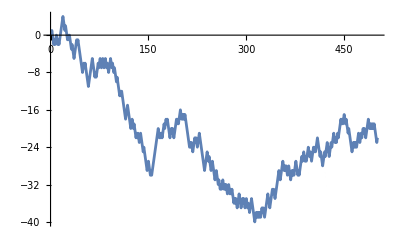

```mathematica
ListLinePlot[NestList[#+RandomChoice[{+1,-1}]&,0,500]]
```

除了“迭代”，还可以递归

```mathematica
NestList[Framed[Grid[{{#,#},{#,#}}]]&,x,3]
```

{x,x | x
x | x,x | x
x | x | x | x
x | x
x | x
x | x | x | x
x | x,x | x
x | x | x | x
x | x
x | x
x | x | x | x
x | x | x | x
x | x | x | x
x | x
x | x
x | x | x | x
x | x
x | x
x | x | x | x
x | x
x | x
x | x | x | x
x | x | x | x
x | x | x | x
x | x
x | x
x | x | x | x
x | x}

在列表前后加0，然后加在一起，得到杨辉三角

```mathematica
NestList[Join[{0},#]+Join[#,{0}]&,{1},8]//Grid
```

1 |  |  |  |  |  |  |  | 
1 | 1 |  |  |  |  |  |  | 
1 | 2 | 1 |  |  |  |  |  | 
1 | 3 | 3 | 1 |  |  |  |  | 
1 | 4 | 6 | 4 | 1 |  |  |  | 
1 | 5 | 10 | 10 | 5 | 1 |  |  | 
1 | 6 | 15 | 20 | 15 | 6 | 1 |  | 
1 | 7 | 21 | 35 | 35 | 21 | 7 | 1 | 
1 | 8 | 28 | 56 | 70 | 56 | 28 | 8 | 1

NestGraph

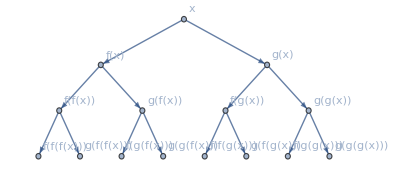

```mathematica
NestGraph[{f[#],g[#]}&,x,3,VertexLabels->All]
```

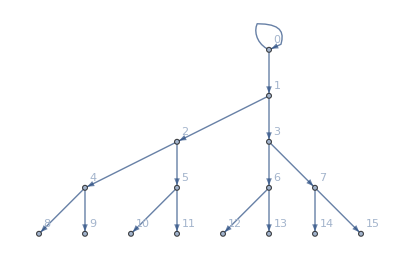

```mathematica
NestGraph[{2 #,2 #+1}&,0,4,VertexLabels->All]
```

“网络爬虫”

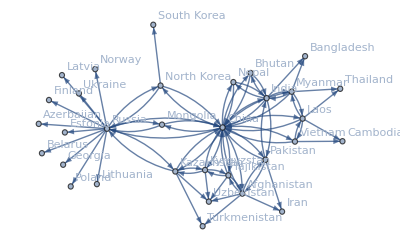

```mathematica
NestGraph[#["BorderingCountries"]&,Entity["Country","China"],2,VertexLabels->All]
```

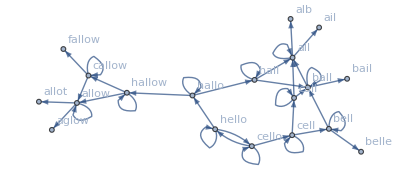

```mathematica
NestGraph[Nearest[WordList[Language->"English"],#,3]&,"hello",4,VertexLabels->All]
```

## 判定和条件

判定素数

```mathematica
Select[Range@1000,PrimeQ]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97,101,103,107,109,113,127,131,137,139,149,151,157,163,167,173,179,181,191,193,197,199,211,223,227,229,233,239,241,251,257,263,269,271,277,281,283,293,307,311,313,317,331,337,347,349,353,359,367,373,379,383,389,397,401,409,419,421,431,433,439,443,449,457,461,463,467,479,487,491,499,503,509,521,523,541,547,557,563,569,571,577,587,593,599,601,607,613,617,619,631,641,643,647,653,659,661,673,677,683,691,701,709,719,727,733,739,743,751,757,761,769,773,787,797,809,811,821,823,827,829,839,853,857,859,863,877,881,883,887,907,911,919,929,937,941,947,953,967,971,977,983,991,997}

判定字母

```mathematica
LetterQ/@Characters["I'm so happy to be programming"]
```

{True,False,True,False,True,True,False,True,True,True,True,True,False,True,True,False,True,True,False,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
Select[Characters["I'm so happy to be programming"],LetterQ]
```

{I,m,s,o,h,a,p,p,y,t,o,b,e,p,r,o,g,r,a,m,m,i,n,g}

回文

```mathematica
Select[WordList[Language->"English"],StringReverse@#==#&]//AbsoluteTiming
```

{0.0603326,{a,aha,bib,bob,civic,dad,deed,did,dud,ere,eve,ewe,eye,gag,gig,huh,I,kayak,kook,level,ma'am,madam,minim,mom,mum,nan,non,noon,nun,oho,pap,peep,pep,pip,pop,pup,radar,refer,rotor,sis,tat,tenet,TNT,toot,tot,tut,wow}}

内置函数判定回文反而更慢……

```mathematica
Select[WordList[Language->"English"],PalindromeQ]//AbsoluteTiming
```

{0.725306,{a,aha,bib,bob,civic,dad,deed,did,dud,ere,eve,ewe,eye,gag,gig,huh,I,kayak,kook,level,ma'am,madam,minim,mom,mum,nan,non,noon,nun,oho,pap,peep,pep,pip,pop,pup,radar,refer,rotor,sis,tat,tenet,TNT,toot,tot,tut,wow}}

含7数

```mathematica
Select[Range[100],MemberQ[IntegerDigits[#],7]&]
```

{7,17,27,37,47,57,67,70,71,72,73,74,75,76,77,78,79,87,97}

猫狗判定

```mathematica
Select[{-Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-}, 
 ImageInstanceQ[#, Entity["Species", "Species:FelisCatus"]] &]
```

{-Graphics-,-Graphics-}

## 重新排列列表

```mathematica
Partition[Range[12],3]
```

{{1,2,3},{4,5,6},{7,8,9},{10,11,12}}

不够3个就直接去掉了

```mathematica
Partition[Range[11],3]
```

{{1,2,3},{4,5,6},{7,8,9}}

可以存在不完整块

```mathematica
Partition[Range[11],UpTo@3]
```

{{1,2,3},{4,5,6},{7,8,9},{10,11}}

把字符排列在网格里

```mathematica
Grid[Partition[Characters["An array of text made in the Wolfram Language"],9],Frame->All]
```

A | n |   | a | r | r | a | y |  
o | f |   | t | e | x | t |   | m
a | d | e |   | i | n |   | t | h
e |   | W | o | l | f | r | a | m
  | L | a | n | g | u | a | g | e

引入一个偏移量

```mathematica
Partition[Range[11],3,1]
```

{{1,2,3},{2,3,4},{3,4,5},{4,5,6},{5,6,7},{6,7,8},{7,8,9},{8,9,10},{9,10,11}}

收集

```mathematica
GatherBy[Characters["It's true that 2+2 is equal to 4!"],LetterQ]
```

{{I,t,s,t,r,u,e,t,h,a,t,i,s,e,q,u,a,l,t,o},{', , , ,2,+,2, , , , ,4,!}}

从连续整数的数字中制作列表

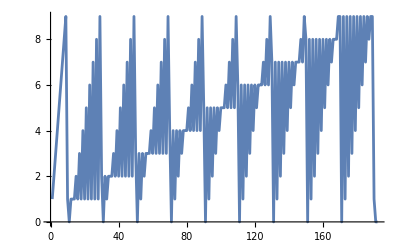

```mathematica
ListLinePlot[Flatten[IntegerDigits/@Range[100]]]
```

ArrayFlatten


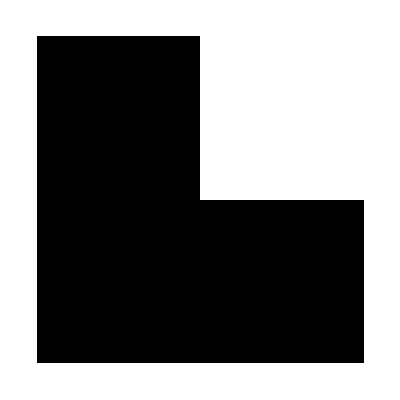
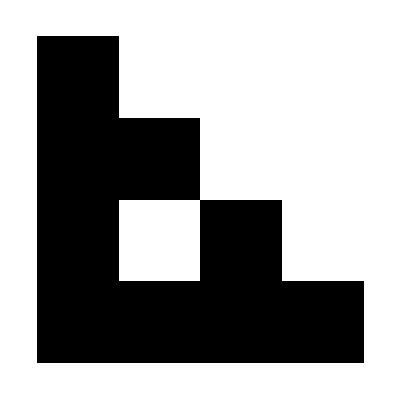
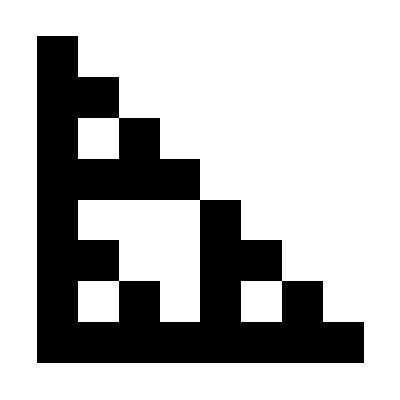
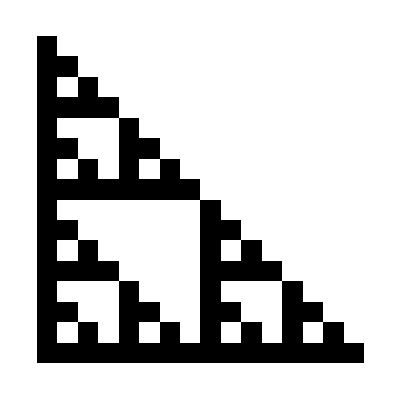

```mathematica
ArrayPlot/@NestList[ArrayFlatten[{{#,0},{#,#}}]&,{{1}},4]
```

```mathematica
ArrayPlot[Nest[ArrayFlatten[{{#,0},{#,#}}]&,{{1}},10]]
```

-Graphics-

集合操作

```mathematica
Union[Alphabet["English"],Alphabet["Swedish"],Alphabet["Turkish"]]
```

{ğ,ş,a,å,ä,b,c,ç,d,e,f,g,h,i,ı,j,k,l,m,n,o,ö,p,q,r,s,t,u,ü,v,w,x,y,z}

```mathematica
Intersection[Alphabet["English"],Alphabet["Swedish"],Alphabet["Turkish"]]
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,r,s,t,u,v,y,z}

```mathematica
Complement[Alphabet["Swedish"],Alphabet["English"]]
```

{å,ä,ö}

元素间插入内容

```mathematica
StringJoin[Riffle[Characters["WOLFRAM"],"--"]]
```

W--O--L--F--R--A--M

排列

```mathematica
Permutations[{Red,Green,Blue}]
```

{{RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1]},{RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 1, 0]},{RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1]},{RGBColor[0, 1, 0],RGBColor[0, 0, 1],RGBColor[1, 0, 0]},{RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[0, 1, 0]},{RGBColor[0, 0, 1],RGBColor[0, 1, 0],RGBColor[1, 0, 0]}}

子集

```mathematica
Subsets[{Red,Green,Blue}]
```

{{},{RGBColor[1, 0, 0]},{RGBColor[0, 1, 0]},{RGBColor[0, 0, 1]},{RGBColor[1, 0, 0],RGBColor[0, 1, 0]},{RGBColor[1, 0, 0],RGBColor[0, 0, 1]},{RGBColor[0, 1, 0],RGBColor[0, 0, 1]},{RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1]}}

三元组

```mathematica
Tuples[{Red,Green},3]
```

{{RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0]},{RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0]},{RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0]},{RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0]},{RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0]},{RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0]},{RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0]},{RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0]}}

随机选择

```mathematica
RandomChoice[{Red,Green,Blue},50]
```

{RGBColor[0, 1, 0],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0]}

```mathematica
RandomChoice[{Red,Green,Blue},{5,3}]
```

{{RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0]},{RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0]},{RGBColor[0, 1, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1]},{RGBColor[0, 0, 1],RGBColor[0, 1, 0],RGBColor[0, 1, 0]},{RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0]}}

随机选择

```mathematica
RandomSample[Range[100],20]
```

{94,85,57,66,90,33,22,64,49,40,88,80,17,51,99,71,55,29,12,69}

随机排列

```mathematica
RandomSample[Range[100]]
```

{1,84,61,33,24,40,64,100,28,8,73,62,75,9,69,87,29,81,22,57,53,78,70,86,3,11,65,17,46,36,58,99,14,23,39,60,15,2,38,51,67,21,76,30,80,89,7,95,59,26,88,82,42,83,72,63,56,41,90,45,68,19,52,97,6,43,93,5,34,16,71,47,91,85,48,37,98,79,54,10,94,31,4,13,77,66,92,74,27,18,96,35,25,49,12,55,32,50,44,20}